# Example Data

As with many functions in the Wolfram Language, additional information (or meta-information) can be assessed with the string argument, “Properties”

```mathematica
ExampleData[{"Statistics","EmployeeAttitude"},"Properties"]
```

# Cases

The pattern matching capabilities of the language makes it fairly easy to extract elements of a list based on patterns and conditions:

```mathematica
data1={{1,"UK",34,"string"},{6,"US",45,0}};
Cases[
data1,
{_,_,age_,value_String}/;age>30]
```

However, when Associations have been introduced to the Wolfram Language as a database like object - requiring the use Queries

# Constructing Associations

There are a multitude of different approaches to constructing expressions - let us consider the simplest here:

```mathematica
columnNames={"Key 1","Key2","Other Key"};
data=RandomInteger[5,{5,3}];
```

```mathematica
Table[AssociationThread[columnNames,data[[i]]],{i,Length[data]}]
```

When querying associations, it’s possible to use named slots

```mathematica
Query[Select[Slot["Key 1"]==2&]]@assocs
```

# Exercises

## RandomVariates, Cases and Pattern Replacements

This question recaps function definitions, introduces RandomVariate and Cases.

Refer to the documentation for RandomVariate and write a function to generate n random variates from a normal distribution with mean m and standard deviation sd

The function should, when given the following input return a list containing 10 elements from a normal distributiin with mean 0 and standard deviation 1

```mathematica
yourFunction[10,0,1]
```

Use the function Cases to return all elements that are less than zero

Cases is only useful for returning elements. The Position function could be used to find the relative positions of offending elements and replace them, but this is inefficient.

Replacement rules use the same pattern matching syntax already introduced, use the following examples to answer the questions below (remember that selecting an expression you don’t recognise and pressing F1 will bring up the documentation)

```mathematica
{"a","aa","bb","c","ccc"}/.a_String/;StringLength[a]>1->"long string"
```

```mathematica
ReplaceAll[{"a","aa","bb","c","ccc"},a_String/;StringLength[a]>1->"long string"]
```

{a,long string,long string,c,long string}

Use the ReplaceAll function to replace all values less than 0 with 0

## Rows and Columns with Parts

This course does not deeply consider the importation or processing of data, however the following template is provided for your benefit as well as to load data for the this exercises:

Set the working directory using SetDirectory

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop","Exercises"}]]
```

List Files

```mathematica
FileNames[]
```

Import the .csv file

```mathematica
csvimport=Import["small-csv.csv","CSV"];
```

The dataset is quite small:

```mathematica
Grid[csvimport]
```

Name | Age | City of Birth
Jane | 23 | Northampton
Sally | 21 | Bellyinborough
Rita | 25 | Budapest
Louis | 26 | Edinborough
James | 22 | Edinborough
Judy | 26 | Cardiff
Rowan | 28 | Budapest
Mike | 29 | Edinborough
Meriel | 28 | Edinborough
Kevin | 23 | Northampton
Ken | 25 | Budapest
Howard | 26 | Budapest

Use Part (shorthand or longhand) to extract the city of birth column

Use the function Tally to tally the frequency of cities of birth - assigning the data structure to an appropriate variable

Use Part to extract the counts from the Tally to create the following BarChart - make sure there are only as many bars as there are distinct cities

```mathematica
Length@DeleteDuplicates[{"string1","String2","string1","String3"}]
```

3

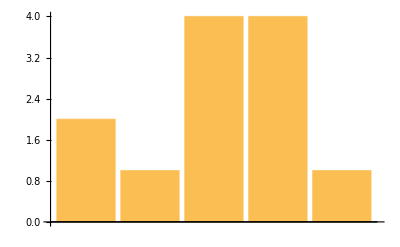

```mathematica
tally=Tally[csvimport[[2;;,-1]]];
BarChart[tally[[All,2]]]
```

Optional steps to make a useful visualisation, skip to the next question if you would prefer to focus on the programming concepts introduced here.

Use the Options ChartLabels and BarOrigin to produce the following chart:

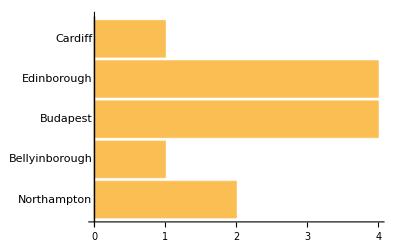

```mathematica
BarChart[tally[[All,2]],
ChartLabels->tally[[All,1]],
BarOrigin->Left]
```

Sort the Tally such that the city(ies) with the largest counts are shown first using SortBy

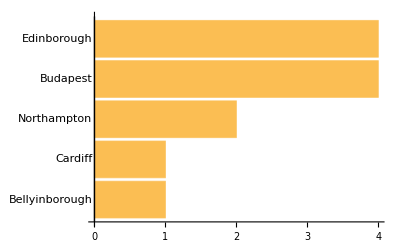

```mathematica
tally=SortBy[tally,#[[2]]&];
BarChart[tally[[All,2]],
ChartLabels->tally[[All,1]],
BarOrigin->Left]
```

## Creating Associations with Table

Use Table to convert the data from this dataset into an association:

```mathematica
ExampleData[{"Statistics","SwissBankNotes"}]
```

Extract the ColumnHeadings and data from ExampleData and assign to appropriate symbols

Use the pattern introduced by the lecturer for converting this data into a list of associations through the following functions:

Table

AssociationThread

```mathematica
headings=ExampleData[{"Statistics","SwissBankNotes"},"ColumnHeadings"];
data=ExampleData[{"Statistics","SwissBankNotes"}];
assocs=Table[AssociationThread[headings->data[[i]]],{i,Length[data]}]
```

## Anonymous Functions

Anonymous functions are extremely useful in the Wolfram Language and are used frequently in code that you’ll find on StackExchange and other resources.

They’re also necessary for performing queries on associations.

Convert the function definition below into a pure function and provide it the argument “ ”

```mathematica
function[a_]:=Riffle[{"You","will","find","this","function","useful"},a]
```

Pure functions are useful in nesting functions

```mathematica
NestList[(1+#)^2&,x,3]
```

{x,(1+x)^2,(1+(1+x)^2)^2,(1+(1+(1+x)^2)^2)^2}

Modify the above function such that it calculates compound interest for a savings account with the following details:

Initial balance of 1000

Annual interest rate of 30%

Three year no-withdrawal (or deposit) limit

```mathematica
NestList[1.3*#&,1000,3]
```

## Querying Associations

If you have succesfully created an association for the SwissBankNotes dataset then use that for this question, otherwise here is a sample of the data:

```mathematica
swissBankNotes={<|"Length"->214.8,"Left"->131,"Right"->131.1,"Bottom"->9,"Top"->9.7,"Diagonal"->141,"Counterfeit"->0|>,<|"Length"->214.6,"Left"->129.7,"Right"->129.7,"Bottom"->8.1,"Top"->9.5,"Diagonal"->141.7,"Counterfeit"->0|>,<|"Length"->214.8,"Left"->129.7,"Right"->129.7,"Bottom"->8.7,"Top"->9.6,"Diagonal"->142.2,"Counterfeit"->0|>,
<|"Length"->215.1,"Left"->129.5,"Right"->129.6,"Bottom"->7.7,"Top"->10.5,"Diagonal"->142.2,"Counterfeit"->0|>,<|"Length"->215.2,"Left"->130.8,"Right"->129.6,"Bottom"->7.9,"Top"->10.8,"Diagonal"->141.4,"Counterfeit"->0|>,<|"Length"->215.5,"Left"->130.4,"Right"->130,"Bottom"->8.2,"Top"->11.2,"Diagonal"->139.2,"Counterfeit"->1|>,<|"Length"->214.7,"Left"->130.6,"Right"->130.1,"Bottom"->11.8,"Top"->10.5,"Diagonal"->139.8,"Counterfeit"->1|>,<|"Length"->214.7,"Left"->130.4,"Right"->130.1,"Bottom"->12.1,"Top"->10.4,"Diagonal"->139.9,"Counterfeit"->1|>,<|"Length"->214.8,"Left"->130.5,"Right"->130.2,"Bottom"->11,"Top"->11,"Diagonal"->140,"Counterfeit"->1|>};
```

Extract the lengths of counterfeit and non-counterfeit bank notes

Calculate the mean of these two dataset - how different are they?

Recalling that “Properties” is a useful way to explore objects, first extract the test conclusion from the object below and then use this pattern to test whether the counterfeit and non-counterfeit bank notes could be differentiated based on their length.

```mathematica
ttest=TTest[{{13,10,10,11,4},{12,5,4,5,2}},Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

How direct (minimal number of steps) a query can you build to find the mean length of counterfeit notes?

```mathematica
(*multiple steps*)
counterfeits=Query[Select[#"Counterfeit"==1&]]@swissBankNotes;
counterfeits[[All,"Length"]]//Mean
```

214.925

```mathematica
(*single query*)
Query[Select[#"Counterfeit"==1&]/*Mean,"Length"]@swissBankNotes
```

214.925

## More Queries

It is useful to have example data sets to learn how functions work, use the skills learned previously to create and then filter a dataset with the following structure:

```mathematica
testAssociation={
<|"Category"->"A","Size"->10,"Users"->1021,"Interactions"->12|>,
...
}
```

Use Table to create a list of associations with 50 individuals in it, the following template will help ypu

```mathematica
Table[{{"Key 1","Value"},{"Key 2",RandomInteger[10]}},5]
```

{{{Key 1,Value},{Key 2,9}},{{Key 1,Value},{Key 2,7}},{{Key 1,Value},{Key 2,0}},{{Key 1,Value},{Key 2,4}},{{Key 1,Value},{Key 2,4}}}

Ensure your association’s keys have the following properties:

“Category” should make a random choice from {“A”,”B”,”C”,”D”}

“Size” should be a random integer between 5 and 50

“Users” should be a random variate from a NormalDistribution with a mean of 1500 and standard deviation of 400

“Interactions” should be a random variate from the following: SkewNormalDistribution[10,5,-6]

Write a query that only selects those entries where “Category” is “A” OR “B”

Write a query that selects all entries with greater than 8 “Interactions” and a “Size” greater than 11 from “Category” “C” and “D”

Tally the number of individuals in each category and display the results in a BarChart